```mathematica
SetDirectory@NotebookDirectory[];
```

#### Potential and Hamiltonian

```mathematica
a=2.6;
b=-1;
V[q_]=a*q^2+b*q^3;
H[q_,p_,t_]=p^2/2+V[q];
```

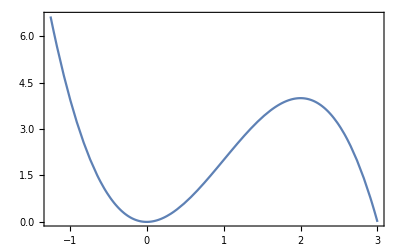

```mathematica
Plot[V[q],{q,-1.25,3},Frame->True,LabelStyle->{Black,18}]
```

```mathematica
(*Local maximum and minimum*)
sol=NSolve[D[V[q],q]==0,q];
xminloc=q/. sol[[1]]
xmaxloc=q/. sol[[2]]
Emaxloc=V[xmaxloc]
```

0.

1.73333

2.60385

#### Classical phase space

```mathematica
(*H1*)
pin=0.0;
qin=xmaxloc-10^(-3);
tf=5000;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
tint=0.1;
(*qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,tint}];*)
qpr=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,tint}];
```

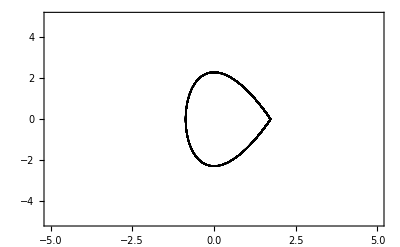

```mathematica
sep=ListPlot[{qpr},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-5,5},{-5,5}},LabelStyle->{16,Black}]
```

#### Wigner function

```mathematica
datawigner=Import["output/Wigner_MetastableState.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

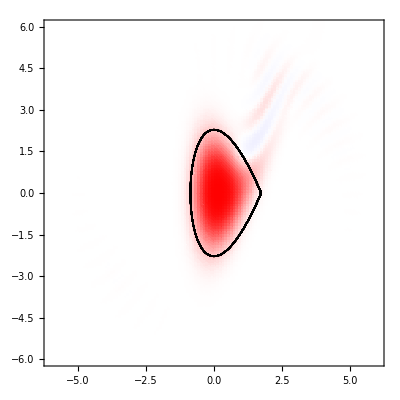

```mathematica
wigner=Show[ListDensityPlot[datawigner,PlotRange->{{-6,6},{-6,6},All},Frame->True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/0.35(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],sep]
```

```mathematica
(*Corroborate that it coincides in the julia script*)
xpint=0.1;
```

```mathematica
(*Total Wigner volume*)
Wvol=0;
Do[Wvol = Wvol + xpint^2*datawigner[[i,3]],{i,1,Length[datawigner]}];
Wvoln=Wvol/Wvol;
Print[Wvoln]
```

1.

```mathematica
(*Total Wigner negativity volume*)
Wabs=0;
Do[Wabs = Wabs + xpint^2*Abs[datawigner[[i,3]]],{i,1,Length[datawigner]}];
Wneg=(Wabs-Wvol)/Wvoln;
Print[Wneg]
```

0.0597357

```mathematica
(*Wigner volume inside the well*)
Wvolin=0;
Do[enerinst=H[datawigner[[i,1]],datawigner[[i,2]],0];
If[(enerinst>0&&enerinst<Emaxloc),
Wvolin = Wvolin + xpint^2*datawigner[[i,3]]],{i,1,Length[datawigner]}];
Wvolinn=Wvolin/Wvol;
Print[Wvolinn]
```

0.925164

```mathematica
(*Wigner negativity volume inside the well*)
Wabsvolin=0;
Do[enerinst=H[datawigner[[i,1]],datawigner[[i,2]],0];
If[(enerinst>0&&enerinst<Emaxloc),
Wabsvolin = Wabsvolin + xpint^2*Abs[datawigner[[i,3]]]],{i,1,Length[datawigner]}];
Wabsvolinn=(Wabsvolin-Wvolin)/Wvol;
Print[Wabsvolinn]
```

0.000405443

```mathematica
(*Wigner volume outside the well*)
Wvolout=0;
Do[enerinst=H[datawigner[[i,1]],datawigner[[i,2]],0];
If[(enerinst<0||enerinst>Emaxloc),
Wvolout= Wvolout + xpint^2*datawigner[[i,3]]],{i,1,Length[datawigner]}];
Wvoloutn=Wvolout/Wvol;
Print[Wvoloutn]
```

0.0718498

```mathematica
(*Wigner negativity volume outside the well*)
Wabsvolout=0;
Do[enerinst=H[datawigner[[i,1]],datawigner[[i,2]],0];
If[(enerinst<0||enerinst>Emaxloc),
Wabsvolout = Wabsvolout+ xpint^2*Abs[datawigner[[i,3]]]],{i,1,Length[datawigner]}];
Wabsvoloutn=(Wabsvolout-Wvolout)/Wvol;
Print[Wabsvoloutn]
```

0.0611871